# Cavity method and ODE simulation in multi-trophic ecosystems

created by Zhijie Feng, contact : zjfeng@bu.edu

Article Source: Emergent competition shapes top-down versus bottom-up control in multi-trophic ecosystems
Feng Z, Marsland R III, Rocks JW, Mehta P (2024) Emergent competition shapes top-down versus bottom-up control in multi-trophic ecosystems. PLOS Computational Biology 20(2): e1011675. https://doi.org/10.1371/journal.pcbi.1011675

## Paper Abstract

Ecosystems are commonly organized into trophic levels -- organisms that occupy the same level in a food chain (e.g., plants, herbivores, carnivores). A fundamental question in theoretical ecology is how the interplay between trophic structure, diversity, and competition shapes the properties of ecosystems. To address this problem, we analyze a generalized Consumer Resource Model with three trophic levels using the zero-temperature cavity method and numerical simulations. We find that intra-trophic diversity gives rise to “emergent competition’’ between species within a trophic level due to feedbacks mediated by other trophic levels. This emergent competition gives rise to a crossover from a regime of top-down control (populations are limited by predators) to a regime of bottom-up control (populations are limited by primary producers) and is captured by a simple order parameter related to the ratio of surviving species in different trophic levels. We show that our theoretical results agree with empirical observations, suggesting that the theoretical approach outlined here can be used to understand complex ecosystems with multiple trophic levels.

## Introduction

### ODE model for ecological dynamics

In the paper, we proposed a set of coupled ODE equations for the consumer-resource dynamics of a 3-trophic-level ecosystems.



 where  is a  matrix of consumer preferences for the the  primary consumers and  is a  matrix of consumer preferences for the  secondary consumers,and  account for finite efficiency of biomass conversion.When  and  are close to one, energy is very efficiently transferred across trophic levels.In contrast,when these values are close to zero,energy cannot be efficiently harvested from lower trophic levels.We also define the carrying capacity  for each primary producer ,along with the death ratesfor each primary consumer  and  for each secondary consumer. 
In this notebook, we consider the case where the consumer preferences  are drawn independently and identically with mean  and standard deviation .We parameterize the variation in  in terms of the random variables  so that
,,.
Similarly,we draw the consumer preferences  independently and identically with mean and standard deviation ,parameterized in terms of the random variables ,
,.
For convenience,we choose to scale the means and variances of the consumer preferences with the number of species, or .We note that this does not affect the generality of our results,but greatly simplifies the mathematical treatment in the thermodynamic limit.

## Example of dynamics

Here we choose a specific set of model parameters, define the numerical,plot one example of the dynamics. Each line represent the biomass of one species in each trophic levels.

```mathematica
(*Define function for ODE simulation*)
FullSimulate[topspecies_,r1_,r2_,k_,m_,u_,sigmak_,sigmam_,sigmau_,muc_,mud_,sigmac_,sigmad_,tfinal_]:=Module[{},
middlespecies=Round[topspecies/r1];
resources=Round[topspecies/r1/r2];

iniX=RandomReal[{1,2},{topspecies}];
inin=RandomReal[{1,2},{middlespecies}];
iniR=RandomReal[{1,2},{resources}];

Dm=RandomVariate[NormalDistribution[mud/middlespecies,sigmad/Sqrt[middlespecies]],{topspecies,middlespecies}];
Cm=RandomVariate[NormalDistribution[muc/resources,sigmac/Sqrt[resources]],{middlespecies,resources}];
us=RandomVariate[NormalDistribution[u,sigmau],topspecies];
ms=RandomVariate[NormalDistribution[m,sigmam],middlespecies];
ks=RandomVariate[NormalDistribution[k,sigmak],resources];
eqns={X'[t]==X[t](Dm.n[t]-us),n'[t]==n[t](Cm.R[t]-ms-Transpose[Dm].X[t]),R'[t]==R[t](ks-R[t]-Transpose[Cm].n[t]),X[0]==iniX,n[0]==inin,R[0]==iniR};
solution=NDSolve[eqns,{X,n,R},{t,tfinal},Method->"StiffnessSwitching"][[1]];

AllR=Table[Evaluate[R[t]/.solution],{t,0,tfinal,0.1}];
Alln=Table[Evaluate[n[t]/.solution],{t,0,tfinal,0.1}];
AllX=Table[Evaluate[X[t]/.solution],{t,0,tfinal,0.1}];
{AllR,Alln,AllX}
];
```

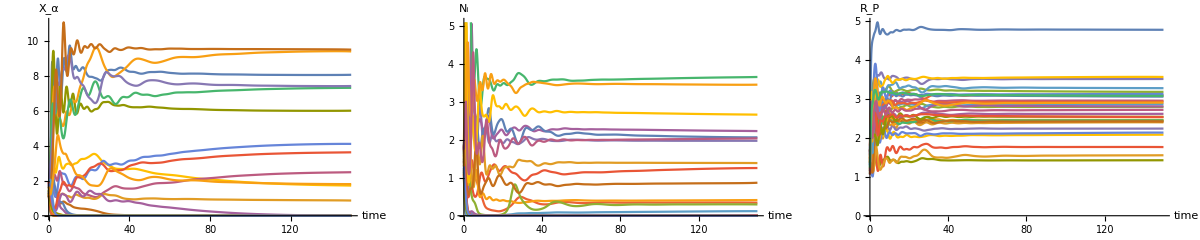

```mathematica
(*Specify parameters for ODE simulation and make a plot of dynamics*)
Endtime=150;
topspecies=30;
sigmau=0.1;
sigmam=0.1;
sigmak=0.1;
u=1;
m=1;
k=4;
sigmac=0.5;
muc=1;
sigmad=0.5;
mud=1;
r1=1;
r2=1;

Dynamics=FullSimulate[topspecies,r1,r2,k,m,u,sigmak,sigmam,sigmau,muc,mud,sigmac,sigmad,Endtime];
Rdynamics=Table[Dynamics[[1,All,alpha]],{alpha,1,Length[Dynamics[[1,1,All]]]}];
Ndynamics=Table[Dynamics[[2,All,alpha]],{alpha,2,Length[Dynamics[[1,2,All]]]}];
Xdynamics=Table[Dynamics[[3,All,alpha]],{alpha,3,Length[Dynamics[[1,3,All]]]}];
Show[GraphicsRow[{ListLinePlot[Xdynamics,AxesLabel->{"time","X_α"},DataRange->{0,Endtime},AspectRatio->0.5],ListLinePlot[Ndynamics,AxesLabel->{"time","N_i"},DataRange->{0,Endtime},AspectRatio->0.5],ListLinePlot[Rdynamics,AxesLabel->{"time","R_P"},DataRange->{0,Endtime},AspectRatio->0.5]}],ImageSize->Full]
```

## Compare cavity method prediction and simulation

### Self-consistency equations from cavity method

The statistics of steady states of the model defined in the previous section can be calculated using cavity method. The result is a set of self-consistency equations with 9 equations for 9 variables,
 
   
   ,
where
,
and we define the integrals
.
Then the  moment of truncated Gaussian ,with positive,can be written in terms of the integral
. These self-consistency equations need to be solved numerically in general

#### Define functions for Gaussian integrals

Here we define the integrals for the 0, 1 and 2nd moment of truncated Gaussians  as functions. We directly use the result from Integration in terms of error function speed up the code.

```mathematica
w1[d_]:=(ⅇ^(-d^2/2)+d √(π/2) (1+Erf[d/(√2)]))/(√(2 π))
w0[d_]:=1/2 (1+Erf[d/(√2)])
W[d_]:=((ⅇ^(-d^2/2)+d √(π/2) (1+Erf[d/(√2)]))^2)/(√(2 π) (d ⅇ^(-d^2/2)+(1+d^2) √(π/2) (1+Erf[d/(√2)])))
```

#### Define cavity solver

We define the solver “Wholesolve” for self consistency equations from cavity method.

```mathematica
sigmau=0.1;
sigmam=0.1;
sigmak=0.1;

u=1;
m=1;
k=4;

sigmac=0.5;
muc=1;
sigmad=0.5;
mud=1;


Wholesolve[r1_,r2_,k_,m_,u_,sigmak_,sigmam_,sigmau_,muc_,mud_,sigmac_,sigmad_](*Here we define the solver for cavity equations*):={

Sigmaue[qn_]:=Sqrt[sigmad^2 qn+sigmau^2];
Sigmame[qr_,qx_]:=Sqrt[sigmac^2 qr+sigmad^2 r1 qx+sigmam^2];
Sigmake[qn_]:=Sqrt[sigmak^2+sigmac^2r2 qn ];

Deltaue[qn_,n_]:=-(u-mud  n)/Sqrt[sigmad^2 qn+sigmau^2];
Deltame[x_,R_,qx_,qr_]:=-(m+r1 mud x-muc R)/Sqrt[sigmac^2 qr+sigmad^2 r1 qx+sigmam^2];
Deltake[n_,qn_]:=(k-muc r2 n)/Sqrt[sigmak^2+sigmac^2r2 qn ];

deltaue=Deltaue[qn,n];
deltame=Deltame[x,R,qx,qr];
deltake=Deltake[n,qn];
sigmaue=Sigmaue[qn];
sigmame=Sigmame[qr,qx];
sigmake=Sigmake[qn];

sus=Solve[{0==X-w0[deltaue]/(sigmad^2 V),0==V+ w0[deltame]/(sigmac^2Ka-r1 sigmad^2 X),0==Ka-w0[deltake]/(1-r2 sigmac^2 V)},{X,V,Ka}][[1]];

Fullfunction={x+sigmaue/(sigmad^2V+0.000000000000000000001) w1[deltaue],n-sigmame/(sigmac^2 Ka-r1 sigmad^2 X+0.000000000000000000001) w1[deltame],R-sigmake/(1-r2 sigmac^2 V+0.000000000000000000001)w1[deltake],
qx-x^2/W[deltaue],
qn-n^2/W[deltame],
qr-R^2/W[deltake]}/.sus;

{x,qx,n,qn,R,qr,w0[deltaue],w0[deltame],w0[deltake]}/.NMinimize[{Fullfunction.Fullfunction,{R>0&&n>0&&x>0&&qr>0&&qn>0&&qx>0&&-w0[Deltaue[qn,n]]+1/r1*w0[Deltame[x,R,qx,qr]]>0}},{{R,0.1,1},{n,0.1,1},{x,0.1,1},{qr,0.1,1},{qn,0.1,1},{qx,0.1,1}},AccuracyGoal->7,PrecisionGoal->6,MaxIterations->30000][[2]]}[[1]];
```

### Plot the distribution of biomass from repeated simulations, and compare to cavity result

Histogram::hbins: The bin specification Automatic cannot be used to determine either how many or which bins to use.

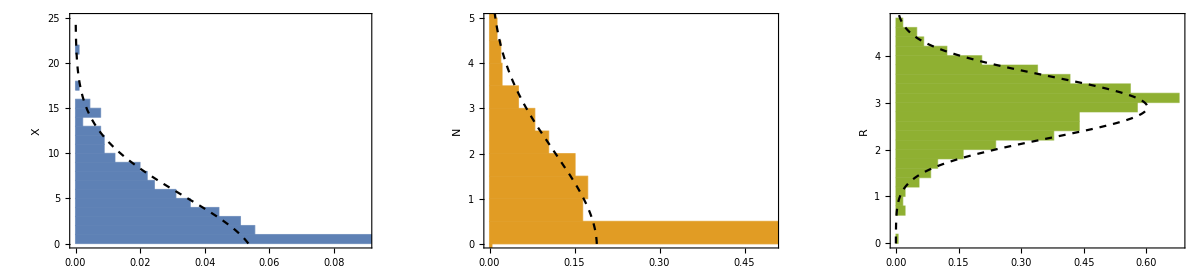

```mathematica
Totalrepeats=30;
Alldatas=Table[FullSimulate[topspecies,r1,r2,k,m,u,sigmak,sigmam,sigmau,muc,mud,sigmac,sigmad,Endtime][[All,-1]],{repeat,1,Totalrepeats}]; (*Here we draw from many systems*)
onesolution=Wholesolve[r1,r2,k,m,u,sigmak,sigmam,sigmau,muc,mud,sigmac,sigmad];(*evaluate cavity result*)

Cavitydistribution[x_,qx_,n_,qn_,R_,qr_,phiX_,phiN_,phiR_,u_,m_,k_,r1_,r2_](*a function that take the cavity solution and output mean and variance of biomass distributions*):=Module[{},
Varx=qx;
Varn=qn;
Varr=qr;
keff=k-muc r2 n;
meff=-m-r1 mud x+muc R;
ueff=-u+mud n;
sigmakeff=Sqrt[sigmak^2+sigmac^2r1 qn];
sigmameff=Sqrt[sigmac^2qr+r1 sigmad^2 qx+sigmam^2];
sigmaueff=Sqrt[sigmau^2+sigmad^2 qn];
g=phiR/r1/r2;
b=phiN/r1;
w=phiX;
f=(g+w-b)/(b-w);
Dx=sigmad^2 /sigmac^2 /r2/f;
Dn=sigmac^2 r2 f phiN;
Dr=1+1/f;
{keff/Dr,sigmakeff/Dr,meff/Dn,sigmameff/Dn, ueff/Dx,sigmaueff/Dx}
]
cavityresult=Cavitydistribution[onesolution[[1]],onesolution[[2]],onesolution[[3]],onesolution[[4]],onesolution[[5]],onesolution[[6]],onesolution[[7]],onesolution[[8]],onesolution[[9]],1,1,4,1,1];
hx=Show[Histogram[Flatten[Alldatas[[All,3]]],"Automatic","PDF",PlotRange-> {{0,0.09},{0.01,25}},BarOrigin->Left,ChartStyle->ColorData[97,"ColorList"][[1]],FrameLabel->{"","X"},Frame->{{True,False},{True,False}}],ParametricPlot[{(ⅇ^(-(-cavityresult[[5]]+x)^2/(2 cavityresult[[6]]^2)))/(cavityresult[[6]] √(2 π)),x},{x,0,25},PlotRange->All,PlotStyle->{Black,Dashed}]];
hn=Show[Histogram[Flatten[Alldatas[[All,2]]],"Automatic","PDF",PlotRange-> {{0,0.5},{0.01,5}},BarOrigin->Left,ChartStyle->ColorData[97,"ColorList"][[2]],FrameLabel->{"","N"},Frame->{{True,False},{True,False}}],ParametricPlot[{(ⅇ^(-(-cavityresult[[3]]+x)^2/(2 cavityresult[[4]]^2)))/(cavityresult[[4]] √(2 π)),x},{x,0,25},PlotRange->All,AspectRatio->1.2,PlotStyle->{Black,Dashed}]];
hr=Show[Histogram[Flatten[Alldatas[[All,1]]],30,"PDF",BarOrigin->Left,ChartStyle->ColorData[97,"ColorList"][[3]],FrameLabel->{"","R"},Frame->{{True,False},{True,False}},PlotRange->All,FrameLabel->{"","R"},Frame->{{True,False},{True,False}}],ParametricPlot[{(ⅇ^(-(-cavityresult[[1]]+x)^2/(2 cavityresult[[2]]^2)))/(cavityresult[[2]] √(2 π)),x},{x,0,25},PlotRange->1,AspectRatio->1.2,PlotStyle->{Black,Dashed}]];
Show[GraphicsRow[{hx,hn,hr},ImageSize->Full],PlotLabel->"Histograms for simulation, dash lines for cavity predictions"]
```

## Plotting phase diagrams from cavity predictions

### Evaluate cavity solution for a range of parameters and save the result

Here we set the range of parameters, evaluate the cavity equations in the range, and save them.

```mathematica
r1start=0.4;
r1end=1.2;
r1interval=(r1end-r1start)/1;
r1list=N[Range[r1start,r1end,r1interval]];

r2start=0.4;
r2end=1.2;
r2interval=(r2end-r2start)/1;
r2list=N[Range[r2start,r2end,r2interval]];

sigmac=0.5;
sigmad=0.5;
numsigmac=1;
numsigmad=1;

(*to vary sigmas, delete the above 4 lines and uncomment the code below *)

(*sigmastart=1;
sigmaend=2.5;
sigmainterval=(sigmaend-sigmastart)/5;
sigmalist=N[Range[sigmastart,sigmaend,sigmainterval]];
numsigmac=Length[sigmalist];
numsigmad=Length[sigmalist];*)

kstart=2;
kend=5;
kinterval=(kend-kstart)/7;
klist=N[Range[kstart,kend,kinterval]];


ustart=1;
uend=3;
uinterval=(uend-ustart)/7;
ulist=N[Range[ustart,uend,uinterval]];


Allsolutionku=ParallelTable[Wholesolve[r1,r2,k,m,u,sigmak,sigmam,sigmau,muc,mud,sigmac,sigmad],{r1,r1start,r1end,r1interval},{r2,r2start,r2end,r2interval},{k,kstart,kend,kinterval},{u,ustart,uend,uinterval}];

(*to vary sigmas, delete the above line and uncomment the code below *)
(*Allsolutionsigmas=ParallelTable[Wholesolve[r1,r2,k,u,sigmac,sigmad],{r1,r1start,r1end,r1interval},{r2,r2start,r2end,r2interval},{k,kstart,kend,kinterval},{u,ustart,uend,uinterval},{sigmac,sigmastart,sigmaend,sigmainterval},{sigmad,sigmastart,sigmaend,sigmainterval}];*)
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 30000 iterations.

### Get the effective competition and order parameters from the solutions

In the paper, we derived the emergent competition D_eff^X,  D_eff^N,  D_eff^R , and the order parameter D_eff^(N, top)/ D_eff^(N, bottom). They are all functions of the statistics obtained from cavity method. The definitions are

```mathematica
GetDtopbottom[r1_,r2_,Allsolutionku_]:={g=Allsolutionku[[All,All,9]]/r1/r2;
b=Allsolutionku[[All,All,8]]/r1;
w=Allsolutionku[[All,All,7]];
(w/b)}

GetDeff[r1_,r2_,Allsolutionku_]:=
{g=Allsolutionku[[All,All,9]]/r1/r2;
b=Allsolutionku[[All,All,8]]/r1;
w=Allsolutionku[[All,All,7]];
f=(g)/(b-w)-1;
phiN=Allsolutionku[[All,All,8]];

{DXeff=sigmad^2/sigmac^2/f/r2,
DNeff=phiN sigmac^2f r2,
DReff=1+1/f}
}

AllDtopbottom=Table[GetDtopbottom[r1list[[r1index]],r2list[[r2index]],Allsolutionku[[r1index,r2index]]][[1]],{r1index,1,2,1},{r2index,1,2,1}];
AllDX=Table[GetDeff[r1list[[r1index]],r2list[[r2index]],Allsolutionku[[r1index,r2index]]][[1,1]],{r1index,1,2,1},{r2index,1,2,1}];
AllDN=Table[GetDeff[r1list[[r1index]],r2list[[r2index]],Allsolutionku[[r1index,r2index]]][[1,2]],{r1index,1,2,1},{r2index,1,2,1}];
AllDR=Table[GetDeff[r1list[[r1index]],r2list[[r2index]],Allsolutionku[[r1index,r2index]]][[1,3]],{r1index,1,2,1},{r2index,1,2,1}];
```

### Making the plots

Here we plot the effective competition  D_eff^X,  D_eff^N,  D_eff^R , and the order parameter D_eff^(N, top)/ D_eff^(N, bottom) evaluated in the previous section as phase diagrams over varied environmental parameters  and .

```mathematica
opts1={InterpolationOrder->0,DataRange->{{ustart,uend},{kstart,kend}},ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,1}]]&),ImageSize->200,ColorFunctionScaling->False,FrameLabel->{"u","k"},PlotRange->All};(*here we fixed the color scale for all four diagrams to value 0 to 1*)

AllFiguresku=Table[
ListDensityPlot[AllDtopbottom[[3-r1index,r2index]],Evaluate[opts1],PlotLabel->"r1="<>ToString@r1list[[3-r1index]]<>", r2="<>ToString@r2list[[r2index]]],{r1index,1,2,1},{r2index,1,2,1}];Show[GraphicsRow[{GraphicsGrid[AllFiguresku],BarLegend[{"Rainbow",{0,1}}]}],PlotLabel->"Order parameter D_top/(D_bottom+D_top)"]
```

-Graphics-

```mathematica
opts2={InterpolationOrder->0,DataRange->{{ustart,uend},{kstart,kend}},ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,3}]]&),ImageSize->200,ColorFunctionScaling->False,FrameLabel->{"u","k"},PlotRange->All};(*here we fixed the color scale for all four diagrams to value 1 to 3*)
AllDxku=Table[
ListDensityPlot[AllDX[[3-r1index,r2index]],Evaluate[opts2],PlotLabel->"r1="<>ToString@r1list[[3-r1index]]<>", r2="<>ToString@r2list[[r2index]]],{r1index,1,2,1},{r2index,1,2,1}];Show[GraphicsRow[{GraphicsGrid[AllDxku],BarLegend[{"Rainbow",{0,3}}]}],PlotLabel->"effective competition D"]
```

-Graphics-

```mathematica
opts3={InterpolationOrder->0,DataRange->{{ustart,uend},{kstart,kend}},ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,3}]]&),ImageSize->200,ColorFunctionScaling->False,FrameLabel->{"u","k"},PlotRange->All};(*here we fixed the color scale for all four diagrams to value 1 to 3*)
AllDNku=Table[
ListDensityPlot[AllDN[[3-r1index,r2index]],Evaluate[opts3],PlotLabel->"r1="<>ToString@r1list[[3-r1index]]<>", r2="<>ToString@r2list[[r2index]]],{r1index,1,2,1},{r2index,1,2,1}];Show[GraphicsRow[{GraphicsGrid[AllDNku],BarLegend[{"Rainbow",{0,3}}]}],PlotLabel->"effective competition D"]
```

-Graphics-

```mathematica
opts4={InterpolationOrder->0,DataRange->{{ustart,uend},{kstart,kend}},ColorFunction->(ColorData["Rainbow"][Rescale[#,{0,3}]]&),ImageSize->200,ColorFunctionScaling->False,FrameLabel->{"u","k"}};(*here we fixed the color scale for all four diagrams to value 0 to 3*)
AllDRku=Table[
ListDensityPlot[AllDR[[3-r1index,r2index]],Evaluate[opts4],PlotLabel->"r1="<>ToString@r1list[[3-r1index]]<>", r2="<>ToString@r2list[[r2index]]],{r1index,1,2,1},{r2index,1,2,1}];Show[GraphicsRow[{GraphicsGrid[AllDRku],BarLegend[{"Rainbow",{0,3}}]}],PlotLabel->"effective competition D"]
```

-Graphics-